sigmaG vs. thetadiff where SigmaE = 0

```mathematica
data=Import["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/model/data/data_maxPE_ddm.csv","table"];
datavalues=Import["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/model/data/data_maxPEvalue_ddm.csv","table"];
```

```mathematica
s=Table[x,{x,0.1,3,0.1}];
tdiff=Table[x,{x,5,10,0.2}];
data2=Table[{tdiff[[i]],s[[j]],data[[i,j]]},{i,Length[tdiff]},{j,Length[s]}];
datavalues2=Table[{tdiff[[i]],s[[j]],datavalues[[i,j]]},{i,Length[tdiff]},{j,Length[s]}];
```

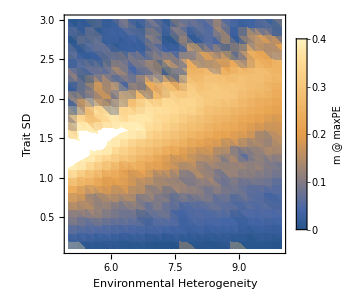

```mathematica
PlotSDH=ListDensityPlot[Flatten[data2,1],PlotRange->{0,0.4},PlotLegends->BarLegend[True,LegendLabel->"m @ maxPE"],FrameLabel->{"Environmental Heterogeneity","Trait SD"},ImageSize->300]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSD.pdf",PlotSDH]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSD.pdf

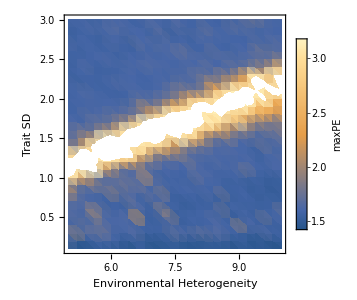

```mathematica
PlotSDHvalue=ListDensityPlot[Flatten[datavalues2,1],PlotLegends->BarLegend[True,LegendLabel->"maxPE"],FrameLabel->{"Environmental Heterogeneity","Trait SD"},ImageSize->300]
```

```mathematica
PlotCombined = GraphicsGrid[{{PlotSDH,PlotSDHvalue}},ImageSize->800]
```

-Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSDcomb_ddm.pdf",PlotCombined]
Export["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSDcomb_ddm.png",PlotCombined,ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSDcomb_ddm.pdf

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSDcomb_ddm.png

h vs. sigG

```mathematica
data=Import["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/model/data/data_maxPE_sigh_ddm.csv","table"];
datavalues=Import["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/model/data/data_maxPEvalue_sigh_ddm.csv","table"];
```

```mathematica
h=Table[x,{x,0.1,1,0.05}];
sig=Table[x,{x,0.1,3,0.1}];
data2=Table[{sig[[i]],h[[j]],data[[i,j]]},{i,1,Length[sig]},{j,1,Length[h]}];
datavalues2=Table[{sig[[i]],h[[j]],datavalues[[i,j]]},{i,1,Length[sig]},{j,1,Length[h]}];
```

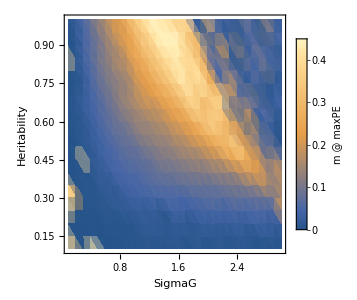

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_HSD.pdf

```mathematica
PlotSDH=ListDensityPlot[Flatten[data2,1],PlotRange->All,PlotLegends->BarLegend[True,LegendLabel->"m @ maxPE"],FrameLabel->{"SigmaG","Heritability"},ImageSize->300]
```

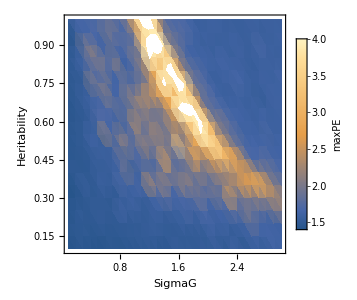

```mathematica
PlotSDHvalue=ListDensityPlot[Flatten[datavalues2,1],PlotRange->{1,4},PlotLegends->BarLegend[True,LegendLabel->"maxPE"],FrameLabel->{"SigmaG","Heritability"},ImageSize->300]
```

```mathematica
PlotCombined = GraphicsGrid[{{PlotSDH,PlotSDHvalue}},ImageSize->800]
```

-Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_heritSDcomb_ddm.png",PlotCombined,ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/fig_heritSDcomb_ddm.png